```mathematica
(*81 lines per section*)
(*r Zr-Zr C-Zr C-C Total*)
```

## Classifier for Frenkel pairs

```mathematica
Ideas to improve the classifier:
1) Each volume has its own classifier
2) Difference the PDF with respect to an average perfect run at that temperature
3) Include Zr-C as well as C-C PDF
4) Include a few steps a high tempertures in the training model
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/collective_PDFs"];
files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt","pdf.PERF.4850.1_1071.txt"};
pdfData=Table[ReadList[files[[i]],{Number,Number,Number,Number,Number}],{i,1,6}];
names={"70","129","142","174","1126","PERF"};
fullNames={"Bound-dimer","Unbound-dimer","Unbound-trimer","Unbound-trimer","Unbound-tetramer","Perfect"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer","Perfect"};
volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};
zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,6}];
```

### PDF plots

```mathematica
ListLinePlot[Partition[zrzr[[1]],81],PlotRange->All];
ListLinePlot[Partition[zrzr[[3]],81],PlotRange->All];
```

```mathematica
Table[ListLinePlot[Partition[cc[[i]],81],PlotRange->All],{i,1,5}];
```

```mathematica
ListLinePlot[Partition[tot[[1]],81][[1;;10]],PlotRange->All];
```

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

### PDF animations

```mathematica
ccAnimation=Table[With[{name=cc},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,PlotLabel->fullNames[[j]],FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,6}];
```

```mathematica
(*Export["B2-test-data-300K.avi",ccAnimation[[1]],"Animation","AnimationRepetitions"->2,"ControlAppearance"->None]*)
plotStyle={PlotRange->{{0,5},{0,.5}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTrainingCC=Table[With[{name=cc},Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[fullNames[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,6}];
framesTrainingCCJoined=Join[framesTrainingCC[[1]],framesTrainingCC[[2]]];
Export["framesTrainingCC.gif",framesTrainingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None,"FrameRate"->25]
```

framesTrainingCC.gif

```mathematica
With[{name=zrzr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

ListAnimate[{},15]

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

## Train classifier

```mathematica
Options@Classify
methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

{1.,0.}

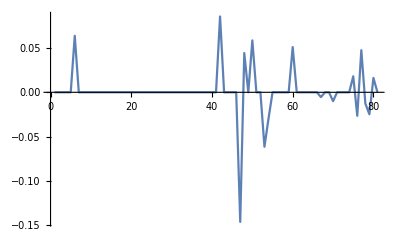

```mathematica
cc[[1]][[1]]
ListLinePlot[Transpose[Partition[cc[[1]],81][[1]]][[2]]-Transpose[Partition[zrzr[[1]],81][[1]]][[2]]]
```

```mathematica
ListAnimate[Table[ListLinePlot[Standardize[Transpose[Partition[cc[[1]],81][[i]]][[2]]-Transpose[Partition[zrzr[[1]],81][[i]]][[2]]],PlotRange->{{0,80},{-5,5}}],{i,1,100}],15]
```

```mathematica
Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,10}],{type,1,2}];
```

```mathematica
Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,10}],{type,1,2}];
```

{0.,0.,0.,0.,0.,0.0637,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0855,0.,0.,0.,0.,0.,0.2216,0.9293,0.3594,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.051,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.018,0.0176,0.1511,0.1818,0.0166,0.0162,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0249,0.,0.,0.,0.0411,0.,0.,0.2972,0.9325,0.29,0.0637,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0268,0.,0.,0.,0.0243,0.0473,0.3234,0.1804,0.0881,0.0215,0.,0.,0.,0.,0.,0.0188,0.,0.,0.,0.,0.,0.0104,0.0061,0.}

#### Standard C-C only

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=100,valSize=1,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Speed"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,1}]];

finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes+1]]},Table[Flatten@Join[{methods[[i]],scores[[i]]}],{i,1,1}]]];
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer
LogisticRegression | 1. | 1. | 1. | 1. | 1.

```mathematica
c[Transpose[Partition[ccTest[[2]],81][[1]]][[2]]]
```

Unbound-trimer

```mathematica
testOut=With[{trainSize=5,valSize=15,maxTypes=2},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-trimer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer

#### Joined C-C and Zr-C

```mathematica
Join[Transpose[Partition[cc[[1]],81][[1]]][[2]],Transpose[Partition[czr[[1]],81][[1]]][[2]]]
```

{0.,0.,0.,0.,0.,0.0637,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0855,0.,0.,0.,0.,0.,0.2216,0.9293,0.3594,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.051,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.018,0.0176,0.1511,0.1818,0.0166,0.0162,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0249,0.,0.,0.,0.0411,0.,0.,0.2972,0.9325,0.29,0.0637,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0268,0.,0.,0.,0.0243,0.0473,0.3234,0.1804,0.0881,0.0215,0.,0.,0.,0.,0.,0.0188,0.,0.,0.,0.,0.,0.0104,0.0061,0.}

```mathematica
methods[[6]]
```

SupportVectorMachine

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=85,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Join[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]],Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Join[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]],Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,6,6}]];

finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes+1]]},Table[Flatten@Join[{methods[[i]],scores[[i]]}],{i,1,Length@scores}]]];
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer
LogisticRegression | 1. | 1. | 1. | 1. | 1.

```mathematica
c[Join[Transpose[Partition[ccTest[[1]],81][[1]]][[2]],Transpose[Partition[zrzrTest[[1]],81][[1]]][[2]]]]
```

Unbound-tetramer

```mathematica
testOut=With[{trainSize=1,valSize=15,maxTypes=2},Table[Table[c@Join[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]],Transpose[Partition[zrzrTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Unbound-tetramer | Unbound-trimer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer

#### Differenced between C-C and Zr-Zr

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=100,valSize=5,method=methods[[i]]},trainSet=Join@@Table[Table[Standardize[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];

trainSet2=With[{trainSizeTest=15,maxTypesTest=2},Join@@Table[Table[Standardize[Transpose[Partition[ccTest[[typeTest]],81][[timeStepTest]]][[2]]-Transpose[Partition[zrzrTest[[typeTest]],81][[timeStepTest]]][[2]]]->fullNames[[1]],{typeTest,1,maxTypesTest}],{timeStepTest,1,trainSizeTest}]];

c=Classify[Join[trainSet,trainSet2],Method->method,PerformanceGoal->"Speed"];
Table[Table[c[Standardize[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,1}]];

finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes+1]]},Table[Flatten@Join[{methods[[i]],scores[[i]]}],{i,1,1}]]];
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer
LogisticRegression | 1. | 1. | 1. | 1. | 1.

```mathematica
testOut=With[{trainSize=1,valSize=30,maxTypes=2},Table[Table[c[Standardize[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzrTest[[type]],81][[timeStep]]][[2]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Unbound-trimer
Bound-dimer | Bound-dimer
Bound-dimer | Unbound-dimer
Bound-dimer | Unbound-dimer
Bound-dimer | Unbound-tetramer
Unbound-tetramer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Bound-dimer
Unbound-dimer | Unbound-trimer
Unbound-dimer | Bound-dimer

## Differenced but not standardised

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=140,valSize=5,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];

trainSet2=With[{trainSizeTest=15,maxTypesTest=2},Join@@Table[Table[Transpose[Partition[ccTest[[typeTest]],81][[timeStepTest]]][[2]]-Transpose[Partition[zrzrTest[[typeTest]],81][[timeStepTest]]][[2]]->fullNames[[1]],{typeTest,1,maxTypesTest}],{timeStepTest,1,trainSizeTest}]];

c=Classify[Join[trainSet,trainSet2],Method->method,PerformanceGoal->"Speed"];
Table[Table[c[Standardize[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzr[[type]],81][[timeStep]]][[2]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,1}]];

finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes+1]]},Table[Flatten@Join[{methods[[i]],scores[[i]]}],{i,1,1}]]];
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer
LogisticRegression | 0.833333 | 1. | 1. | 1. | 1.

```mathematica
testOut=With[{trainSize=1,valSize=95,maxTypes=2},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]-Transpose[Partition[zrzrTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Unbound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-trimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Bound-dimer
Unbound-dimer | Unbound-trimer
Unbound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-trimer | Unbound-tetramer
Unbound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-dimer | Unbound-dimer
Unbound-trimer | Unbound-dimer
Bound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-dimer | Unbound-dimer
Bound-dimer | Unbound-trimer
Bound-dimer | Bound-dimer
Unbound-dimer | Unbound-tetramer
Unbound-trimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-trimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-trimer | Unbound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Unbound-trimer
Unbound-trimer | Unbound-dimer
Unbound-trimer | Unbound-dimer
Unbound-trimer | Unbound-dimer
Unbound-dimer | Unbound-trimer
Unbound-trimer | Bound-dimer
Bound-dimer | Unbound-trimer
Unbound-trimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Unbound-tetramer
Bound-dimer | Unbound-trimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-trimer | Bound-dimer
Bound-dimer | Unbound-dimer
Unbound-tetramer | Unbound-dimer
Bound-dimer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-dimer | Bound-dimer
Bound-dimer | Unbound-tetramer
Bound-dimer | Unbound-tetramer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Bound-dimer
Bound-dimer | Unbound-tetramer
Bound-dimer | Unbound-tetramer
Bound-dimer | Unbound-dimer
Unbound-tetramer | Bound-dimer
Bound-dimer | Bound-dimer
Unbound-tetramer | Unbound-dimer
Unbound-dimer | Unbound-dimer
Unbound-dimer | Bound-dimer
Unbound-trimer | Unbound-dimer
Unbound-dimer | Unbound-tetramer
Unbound-tetramer | Bound-dimer

```mathematica
trainSet2//Length
```

30

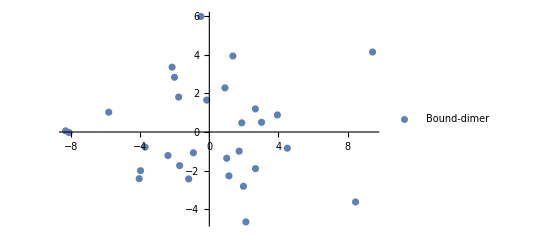

```mathematica
ListPlot[Values[byspecies],PlotLegends->Keys[byspecies]]
```

```mathematica
Partition[trainSet2,15][[1]][[All,1]]//Dimensions
```

{15,81}

```mathematica
features={DimensionReduce[Partition[trainSet2,15][[1]][[All,1]],2],DimensionReduce[Partition[trainSet2,15][[2]][[All,1]],2]};
```

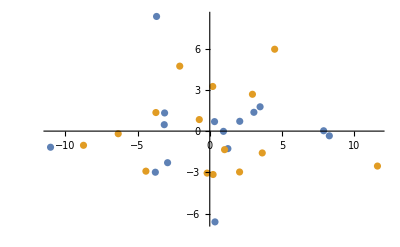

```mathematica
ListPlot@features
```

```mathematica
Values
```

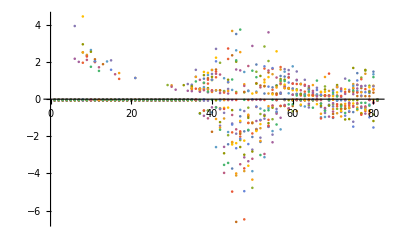

```mathematica
ListPlot[Partition[trainSet2,15][[2]],PlotRange->All]
```

## Import test data

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/test-data"];
filesTest={"1-Frenkel_500_222kp-6hr-9.602/pdf.70.4801.1_866.txt","2-Frenkel_500_222kp-6hr-9.700/pdf.test.4850.1_1021.txt"};
pdfDataTest=Table[ReadList[filesTest[[i]],{Number,Number,Number,Number,Number}],{i,1,2}];
```

```mathematica
zrzrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[2]]},{i,1,2}];
czrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[3]]},{i,1,2}];
ccTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[4]]},{i,1,2}];
totTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[5]]},{i,1,2}];
```

#### PDF plot, animation, and export;

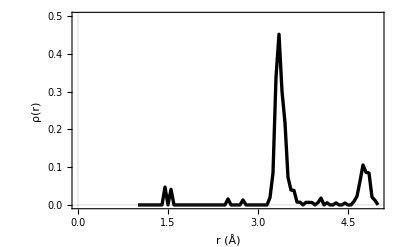

```mathematica
ListLinePlot[Partition[ccTest[[1]],81][[1]],plotStyle]
```

```mathematica
(*ccTestAnimation=Table[With[{name=ccTest},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[volumes[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,2}]*)
```

{,}

```mathematica
(*SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTestingCC=Table[With[{name=ccTest},Table[ListLinePlot[Partition[name[[j]],81][[i]],Frame->True,plotStyle,PlotLabel->Style["3000 K MD",18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,1}];
framesTestingCCJoined=Join[framesTestingCC[[1]],framesTestingCC[[1]]];
Export["framesTestingCC.gif",framesTestingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None]*)
```

framesTestingCC.gif

{Null,Null,Null,Null,Null}

## Apply classifier to test data

```mathematica
c[Transpose[Partition[ccTest[[1]],81][[1]]][[1]]]
```

Unbound-tetramer

```mathematica
testOut=With[{trainSize=1,valSize=5,maxTypes=2},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Unbound-dimer | Unbound-trimer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer

```mathematica
With[{trainSize=1,valSize=150,maxTypes=1},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]]
```

{{Unbound-dimer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-trimer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer},{Unbound-tetramer}}

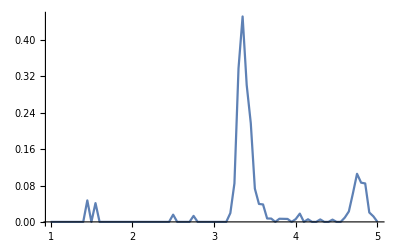

```mathematica
ListLinePlot[{testList},PlotRange->All]
```

```mathematica
train=Table[Partition[cc[[i]],81][[1]],{i,1,5}];
```

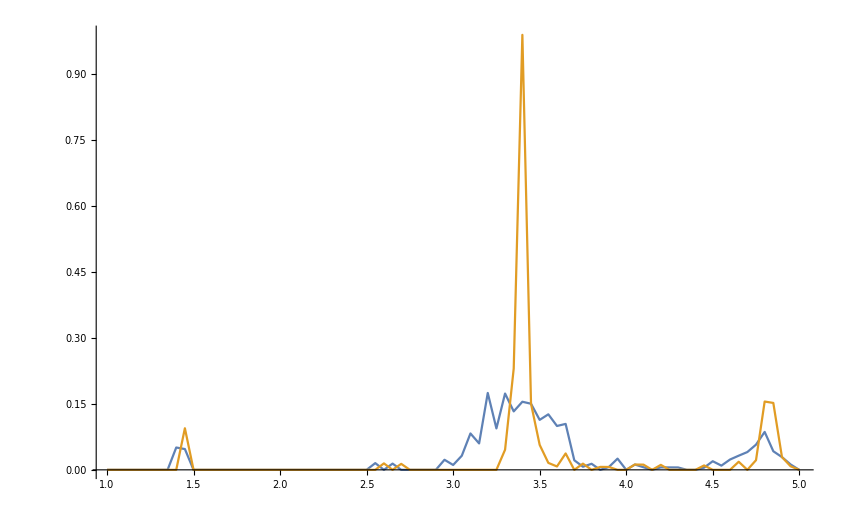

```mathematica
ListLinePlot[{Partition[ccTest[[1]],81][[3]],train[[3]]},PlotRange->All]
```

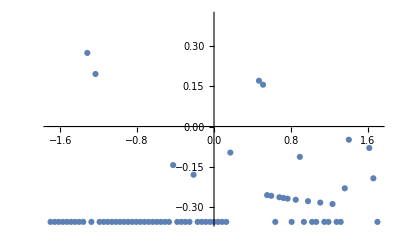

```mathematica
ListPlot@Standardize[testList]
```

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=100,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c2=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c2[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```